```mathematica
Directory[]
```

/home/milan

```mathematica
ψ[μ_,L_]:=∑_(n=0)^L (2n+1)/2 LegendreP[n,μ] Subscript[ϕ, n][z]
```

```mathematica
L=5;
```

Replace Q by ⅆ/ⅆz

```mathematica
P[n_]=(n+1)/(2n+1)Q Subscript[ϕ, n+1][z] +n/(2n+1)Q Subscript[ϕ, n-1][z]+Subscript[Σ, a,n][z]Subscript[ϕ, n][z]==Subscript[S, n][z]
```

(n Q ϕ_(-1+n)[z])/(1+2 n)+((1+n) Q ϕ_(1+n)[z])/(1+2 n)+ϕ_n[z] Σ_(a,n)[z]==S_n[z]

```mathematica
eqns=Table[P[n]/.If[n≥1, Subscript[S, n][z]->0,Subscript[S, n][z]->Subscript[S, n][z]],{n,0,L}]/.Subscript[ϕ, L+1][z]->0;
```

```mathematica
MatrixForm[eqns]
```

(Q ϕ_1[z]+ϕ_0[z] Σ_(a,0)[z]==S_0[z]
1/3 Q ϕ_0[z]+2/3 Q ϕ_2[z]+ϕ_1[z] Σ_(a,1)[z]==0
2/5 Q ϕ_1[z]+3/5 Q ϕ_3[z]+ϕ_2[z] Σ_(a,2)[z]==0
3/7 Q ϕ_2[z]+4/7 Q ϕ_4[z]+ϕ_3[z] Σ_(a,3)[z]==0
4/9 Q ϕ_3[z]+5/9 Q ϕ_5[z]+ϕ_4[z] Σ_(a,4)[z]==0
5/11 Q ϕ_4[z]+ϕ_5[z] Σ_(a,5)[z]==0)

```mathematica
oddn=Table[2n-1,{n,1,(L+1)/2}];
evenn=Table[2n,{n,1,(L+1)/2}];
```

```mathematica
oddmom=Table[Subscript[ϕ, n][z],{n,0,L}][[evenn]]
evenmom=Table[Subscript[ϕ, n][z],{n,0,L}][[oddn]]
```

{ϕ_1[z],ϕ_3[z],ϕ_5[z]}

{ϕ_0[z],ϕ_2[z],ϕ_4[z]}

```mathematica
oddWrtEven=Solve[eqns[[evenn]],oddmom]
```

{{ϕ_1[z]→(-Q ϕ_0[z]-2 Q ϕ_2[z])/(3 Σ_(a,1)[z]),ϕ_3[z]→(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(7 Σ_(a,3)[z]),ϕ_5[z]→-(5 Q ϕ_4[z])/(11 Σ_(a,5)[z])}}

```mathematica
SPL=eqns[[oddn]]/.oddWrtEven[[1]];
```

```mathematica
MatrixForm[SPL]
```

(ϕ_0[z] Σ_(a,0)[z]+(Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(3 Σ_(a,1)[z])==S_0[z]
(2 Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(15 Σ_(a,1)[z])+ϕ_2[z] Σ_(a,2)[z]+(3 Q (-3 Q ϕ_2[z]-4 Q ϕ_4[z]))/(35 Σ_(a,3)[z])==0
(4 Q (-3 Q ϕ_2[z]-4 Q ϕ_4[z]))/(63 Σ_(a,3)[z])+ϕ_4[z] Σ_(a,4)[z]-(25 Q^2 ϕ_4[z])/(99 Σ_(a,5)[z])==0)

```mathematica
oddPseudoFluxes=Table[(n+1) Subscript[ϕ, n+1][z] +n Subscript[ϕ, n-1][z]==Subscript[F, n][z],{n,1,L,2}]/.Subscript[ϕ, L+1][z]->0
pseudoDiffusions=Table[1/((2n+1)Subscript[Σ, a,n][z])->Subscript[D, n][z],{n,1,L,2}]
```

{ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]}

{1/(3 Σ_(a,1)[z])→D_1[z],1/(7 Σ_(a,3)[z])→D_3[z],1/(11 Σ_(a,5)[z])→D_5[z]}

```mathematica
lower=Table[n/(2n+1),{n,2,L,2}]
centr=Table[(n+1)/(2n+1),{n,0,L,2}]
```

{2/5,4/9}

{1,3/5,5/9}

```mathematica
Adata=If[L>1,{Band[{2,1}]->lower,Band[{1,1}]->centr},{Band[{1,1}]->centr}];
```

```mathematica
A=SparseArray[Adata,Floor[L/2]+1];
```

```mathematica
A//Normal//MatrixForm
```

(1 | 0 | 0
2/5 | 3/5 | 0
0 | 4/9 | 5/9)

```mathematica
Map[MatrixForm[#]&,JordanDecomposition[A]]
```

{(0 | 0 | 1
0 | 1/10 | 1
1 | 1 | 1),(5/9 | 0 | 0
0 | 3/5 | 0
0 | 0 | 1)}

```mathematica
rhs=Table[Subscript[Σ, a,n][z]Subscript[ϕ, n][z],{n,0,L,2}];
rhs[[1]]=rhs[[1]]-Subscript[S, 0][z];
```

```mathematica
DelDDelFs=Table[Subscript[DelDDelF, n],{n,1,L,2}];
```

```mathematica
eqnsForDelDDelFs1=Thread[DelDDelFs==LinearSolve[A,rhs]]
```

{DelDDelF_1==-S_0[z]+ϕ_0[z] Σ_(a,0)[z],DelDDelF_3==(2 S_0[z])/3-2/3 ϕ_0[z] Σ_(a,0)[z]+5/3 ϕ_2[z] Σ_(a,2)[z],DelDDelF_5==1/15 (-8 S_0[z]+8 ϕ_0[z] Σ_(a,0)[z]-20 ϕ_2[z] Σ_(a,2)[z]+27 ϕ_4[z] Σ_(a,4)[z])}

```mathematica
eqnsForDelDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDelDDelFs1]
```

{{DelDDelF_1==-S_0[z]+ϕ_0[z] Σ_(a,0)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DelDDelF_3==(2 S_0[z])/3-2/3 ϕ_0[z] Σ_(a,0)[z]+5/3 ϕ_2[z] Σ_(a,2)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DelDDelF_5==1/15 (-8 S_0[z]+8 ϕ_0[z] Σ_(a,0)[z]-20 ϕ_2[z] Σ_(a,2)[z]+27 ϕ_4[z] Σ_(a,4)[z]),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]}}

```mathematica
eqnsForDelDDelFs3=Map[Eliminate[#,evenmom]&,eqnsForDelDDelFs2]
```

{15 DelDDelF_1+15 S_0[z]+10 F_3[z] Σ_(a,0)[z]-8 F_5[z] Σ_(a,0)[z]==15 F_1[z] Σ_(a,0)[z],-45 DelDDelF_3+30 S_0[z]+20 F_3[z] Σ_(a,0)[z]-16 F_5[z] Σ_(a,0)[z]+25 F_3[z] Σ_(a,2)[z]-20 F_5[z] Σ_(a,2)[z]==30 F_1[z] Σ_(a,0)[z],225 DelDDelF_5+120 S_0[z]+80 F_3[z] Σ_(a,0)[z]-64 F_5[z] Σ_(a,0)[z]+100 F_3[z] Σ_(a,2)[z]-80 F_5[z] Σ_(a,2)[z]-81 F_5[z] Σ_(a,4)[z]==120 F_1[z] Σ_(a,0)[z]}

```mathematica
coefAtDs=Thread[Coefficient[eqnsForDelDDelFs3/.Equal->Plus,DelDDelFs]]
```

{15,-45,225}

```mathematica
eqnsForDelDDelFs4=Thread[Thread[Expand[eqnsForDelDDelFs3[[All,1]]/coefAtDs]]==Thread[Expand[eqnsForDelDDelFs3[[All,2]]/coefAtDs]]]
```

{DelDDelF_1+S_0[z]+2/3 F_3[z] Σ_(a,0)[z]-8/15 F_5[z] Σ_(a,0)[z]==F_1[z] Σ_(a,0)[z],DelDDelF_3-(2 S_0[z])/3-4/9 F_3[z] Σ_(a,0)[z]+16/45 F_5[z] Σ_(a,0)[z]-5/9 F_3[z] Σ_(a,2)[z]+4/9 F_5[z] Σ_(a,2)[z]==-2/3 F_1[z] Σ_(a,0)[z],DelDDelF_5+(8 S_0[z])/15+16/45 F_3[z] Σ_(a,0)[z]-64/225 F_5[z] Σ_(a,0)[z]+4/9 F_3[z] Σ_(a,2)[z]-16/45 F_5[z] Σ_(a,2)[z]-9/25 F_5[z] Σ_(a,4)[z]==8/15 F_1[z] Σ_(a,0)[z]}

```mathematica
eqnsForDelDDelFs5=eqnsForDelDDelFs4/.Thread[DelDDelFs->Table[Subscript[DelDDel, n][z]Subscript[F, n][z],{n,1,L,2}]]
```

{DelDDel_1[z] F_1[z]+S_0[z]+2/3 F_3[z] Σ_(a,0)[z]-8/15 F_5[z] Σ_(a,0)[z]==F_1[z] Σ_(a,0)[z],DelDDel_3[z] F_3[z]-(2 S_0[z])/3-4/9 F_3[z] Σ_(a,0)[z]+16/45 F_5[z] Σ_(a,0)[z]-5/9 F_3[z] Σ_(a,2)[z]+4/9 F_5[z] Σ_(a,2)[z]==-2/3 F_1[z] Σ_(a,0)[z],DelDDel_5[z] F_5[z]+(8 S_0[z])/15+16/45 F_3[z] Σ_(a,0)[z]-64/225 F_5[z] Σ_(a,0)[z]+4/9 F_3[z] Σ_(a,2)[z]-16/45 F_5[z] Σ_(a,2)[z]-9/25 F_5[z] Σ_(a,4)[z]==8/15 F_1[z] Σ_(a,0)[z]}

```mathematica
{b,m}=CoefficientArrays[eqnsForDelDDelFs5,Table[Subscript[F, n][z],{n,1,L,2}]]
```

{SparseArray[<3>,{3}],SparseArray[<9>,{3,3}]}

```mathematica
Normal[b]//MatrixForm
```

(S_0[z]
-2/3 S_0[z]
(8 S_0[z])/15)

```mathematica
Normal[m]//MatrixForm
```

(DelDDel_1[z]-Σ_(a,0)[z] | 2/3 Σ_(a,0)[z] | -8/15 Σ_(a,0)[z]
2/3 Σ_(a,0)[z] | DelDDel_3[z]-4/9 Σ_(a,0)[z]-5/9 Σ_(a,2)[z] | 16/45 Σ_(a,0)[z]+4/9 Σ_(a,2)[z]
-8/15 Σ_(a,0)[z] | 16/45 Σ_(a,0)[z]+4/9 Σ_(a,2)[z] | DelDDel_5[z]-64/225 Σ_(a,0)[z]-16/45 Σ_(a,2)[z]-9/25 Σ_(a,4)[z])

```mathematica
F[A_]:=TraditionalForm[A/.{Subscript[DelDDel, n_][z]->Subscript[DelDDel, n],Subscript[Σ, a,n__][z]->Subscript[Σ, n],Subscript[S, 0][z]->Subscript[S, 0]}]
```

```mathematica
F[Normal[m]//MatrixForm]
```

(DelDDel_1-Σ_0 | (2 Σ_0)/3 | -(8 Σ_0)/15
(2 Σ_0)/3 | DelDDel_3-(4 Σ_0)/9-(5 Σ_2)/9 | (16 Σ_0)/45+(4 Σ_2)/9
-(8 Σ_0)/15 | (16 Σ_0)/45+(4 Σ_2)/9 | DelDDel_5-(64 Σ_0)/225-(16 Σ_2)/45-(9 Σ_4)/25)

```mathematica
Normal[m-Transpose[m]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
SuperPlus[j]=Table[∫_0^1 LegendreP[n,μ]ψ[μ,L]ⅆμ,{n,1,L,2}]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256+(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(14 Σ_(a,3)[z]),ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256-(5 Q ϕ_4[z])/(22 Σ_(a,5)[z])}

```mathematica
DDelFs=Table[Subscript[DDelF, n],{n,1,L,2}]
```

{DDelF_1,DDelF_3,DDelF_5}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==2Map[Delete[#,-1]&,SuperPlus[j]]]
```

{DDelF_1==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32),DDelF_3==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256),DDelF_5==2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256)}

```mathematica
eqnsForDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_1==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DDelF_3==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DDelF_5==2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]}}

```mathematica
Map[Eliminate[#,evenmom]&,eqnsForDDelFs2]
```

{16 DDelF_1+2 F_3[z]-F_5[z]==8 F_1[z],-384 DDelF_3+112 F_3[z]-41 F_5[z]==48 F_1[z],1920 DDelF_5+205 F_3[z]-407 F_5[z]==120 F_1[z]}

```mathematica
SuperMinus[j]=Table[∫_-1^0 LegendreP[n,Abs[μ]]ψ[μ,L]ⅆμ//Distribute,{n,1,L,2}]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32-(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(14 Σ_(a,3)[z]),ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(5 Q ϕ_4[z])/(22 Σ_(a,5)[z])}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==-2Map[Delete[#,-1]&,SuperMinus[j]]]
```

{DDelF_1==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32),DDelF_3==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256),DDelF_5==-2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256)}

```mathematica
eqnsForDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_1==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DDelF_3==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]},{DDelF_5==-2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]==F_5[z]}}

```mathematica
Solve[Map[Eliminate[#,evenmom]&,eqnsForDDelFs2],DDelFs]
```

{{DDelF_1→1/16 (-8 F_1[z]+2 F_3[z]-F_5[z]),DDelF_3→1/384 (48 F_1[z]-112 F_3[z]+41 F_5[z]),DDelF_5→(-120 F_1[z]+205 F_3[z]-407 F_5[z])/1920}}

```mathematica
Expand[Flatten[%]]
```

{DDelF_1→-1/2 F_1[z]+F_3[z]/8-F_5[z]/16,DDelF_3→F_1[z]/8-(7 F_3[z])/24+(41 F_5[z])/384,DDelF_5→-1/16 F_1[z]+(41 F_3[z])/384-(407 F_5[z])/1920}

```mathematica
Needs["PlotLegends`"]
```

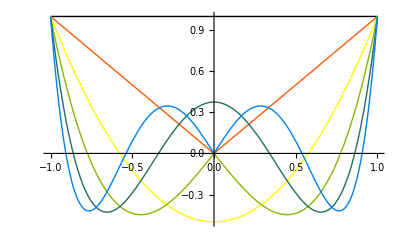

```mathematica
Plot[Evaluate@Table[LegendreP[n,Abs[μ]],{n,0,5}],{μ,-1,1},PlotStyle->ColorData[3,"ColorList"]]
```

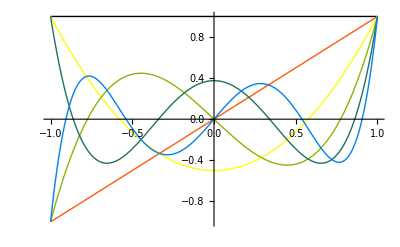

```mathematica
Plot[Evaluate@Table[LegendreP[n,μ],{n,0,5}],{μ,-1,1},PlotStyle->ColorData[3,"ColorList"]]
```

```mathematica
Table[LegendreP[n,μ],{n,0,5}]
```

{1,μ,1/2 (-1+3 μ^2),1/2 (-3 μ+5 μ^3),1/8 (3-30 μ^2+35 μ^4),1/8 (15 μ-70 μ^3+63 μ^5)}

```mathematica
SuperPlus[j]-SuperMinus[j]
```

{(-Q ϕ_0[z]-2 Q ϕ_2[z])/(3 Σ_(a,1)[z]),(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(7 Σ_(a,3)[z]),-(5 Q ϕ_4[z])/(11 Σ_(a,5)[z])}

```mathematica
even=Table[Subscript[ϕ, 2i][z]/.Solve[Eliminate[oddPseudoFluxes,Drop[evenmom,{i+1}]],Subscript[ϕ, 2i][z]]//First//Expand,{i,0,(L-1)/2}]
```

{F_1[z]-(2 F_3[z])/3+(8 F_5[z])/15,F_3[z]/3-(4 F_5[z])/15,F_5[z]/5}

```mathematica
G[S_]:=S/.{Subscript[F, n_][z]->1}
```

```mathematica
Column[{F[Normal[m]]==F[Normal[b]]/.{Subscript[Σ, 0]->0.012,Subscript[Σ, 2]->0.025,Subscript[Σ, 4]->0.025,Subscript[DelDDel, 1]->Lap/(3 0.025),Subscript[DelDDel, 3]->Lap/(7 0.025),Subscript[DelDDel, 5]-> Lap/(11 0.025),Subscript[S, 0]->0.0155 G[First[even]]},
F[Normal[m]]==F[Normal[b]]/.{Subscript[Σ, 0]->0.001,Subscript[Σ, 2]->0.025,Subscript[Σ, 4]->0.025,Subscript[DelDDel, 1]->Lap/(3 0.019),Subscript[DelDDel, 3]-> Lap/(7 0.025),Subscript[DelDDel, 5]-> Lap/(11 0.025),Subscript[S, 0]->0.0},
F[Normal[m]]==F[Normal[b]]/.{Subscript[Σ, 0]->0.075,Subscript[Σ, 2]->0.075,Subscript[Σ, 4]->0.075,Subscript[DelDDel, 1]->Lap/(3 0.075),Subscript[DelDDel, 3]-> Lap/(7 0.075),Subscript[DelDDel, 5]-> Lap/(11 0.075),Subscript[S, 0]->0.0}},Center,1,Dividers->All]
```

(13.3333 Lap-0.012 | 0.008 | -0.0064
0.008 | 5.71429 Lap-0.0192222 | 0.0153778
-0.0064 | 0.0153778 | 3.63636 Lap-0.0213022)=={0.0134333,-0.00895556,0.00716444}
(17.5439 Lap-0.001 | 0.000666667 | -0.000533333
0.000666667 | 5.71429 Lap-0.0143333 | 0.0114667
-0.000533333 | 0.0114667 | 3.63636 Lap-0.0181733)=={0.,0.,0.}
(4.44444 Lap-0.075 | 0.05 | -0.04
0.05 | 1.90476 Lap-0.075 | 0.06
-0.04 | 0.06 | 1.21212 Lap-0.075)=={0.,0.,0.}